### This Mathematica notebook contains the computations for the paper “Unidirectional migration of populations with Allee effect” where the sequence of nonnegative steady states of the system in equation (1) in the paper for fixed values of the Allee threshold parameter, but varying spatial dispersal rate, is computed in the “one way migration” case. Part 2: Right side of Figure 4.

#### This section contains the functions that are used in the next section.

Consider the parametric system of polynomial equations given at equation (2) of the paper with the inequality constraints on the variables and the parameters, and \delta_{1,2}=1, \delta_{2,1}=0.

We define systemEquations to be the list of the two polynomial equations resulted by letting \dot{N_1}=\dot_{N_2}=0 from equation (1).

```mathematica
systemEquations={Subscript[N, 1]*(1-Subscript[N, 1])*(Subscript[N, 1]-b)-a*Subscript[N, 1],Subscript[N, 2]*(1-Subscript[N, 2])*(Subscript[N, 2]-b)+a*Subscript[N, 1]}
```

{-a N_1+(1-N_1) N_1 (-b+N_1),a N_1+(1-N_2) N_2 (-b+N_2)}

The following function in addition to what “solvor” function of the Mathematica notebook part 1 does, substitutes each solution at the Jacobian matrix of the system and computes the eigenvalues to decide stability of these points as steady states.

```mathematica
solvorStability[aa_,bb_]:=(
equations=ReplaceAll[{a->aa,b->bb}][systemEquations];
solutions=NSolve[equations[[1]]==0&&equations[[2]]==0&&Subscript[N, 1]≥0&&Subscript[N, 2]≥0,{Subscript[N, 1],Subscript[N, 2]},Reals];
pointsWithStability=ConstantArray[{{0,0},1},Length[solutions]];
For[i=1,i≤Length[solutions],i++,
pointsWithStability[[i]][[1]]=ReplaceAll[solutions[[i]]][{Subscript[N, 1],Subscript[N, 2]}];
];
JacobM=ConstantArray[0,{2,2}];
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
JacobM[[i,j]]=D[equations[[i]],Subscript[N, j]];
];
];
For[i=1,i≤Length[pointsWithStability],i++,
JacobMSubsed=ReplaceAll[{Subscript[N, 1]->pointsWithStability[[i]][[1]][[1]],Subscript[N, 2]->pointsWithStability[[i]][[1]][[2]]}][JacobM];
EigenvaluesJacobMSubsed=Eigenvalues[JacobMSubsed];
For[j=1,j≤Length[EigenvaluesJacobMSubsed],j++,
If[Re[EigenvaluesJacobMSubsed[[j]]]≥0,{pointsWithStability[[i]][[2]]=0;Break}];
];
];
Return[pointsWithStability];
)
```

The following function finds the critical values of “a” for a fixed given value of “b”. This is done by solving f(a,b)=0 after substituting the given choice of b. Where f is any of the two polynomials defining the boundary between the open regions in Figure 3 of the paper. They are accessible by asking the RootFinding[Parametric] package of Maple to show the algebraic description of the cells.

Note that equation1 and equation2 in below are the two polynomials found in the Maple worksheet, defining the regions boundaries between where the number of steady states changes.

```mathematica
criticalValuesA[bb_]:=(
equation1=ReplaceAll[{b->bb}][16*a^3*b^6+16*a^2*b^7-4*a*b^8+108*a^4*b^4+60*a^3*b^5-75*a^2*b^6+10*a*b^7+b^8-54*a^4*b^3-12*a^3*b^4+42*a^2*b^5+4*a*b^6-4*b^7+729*a^6+1458*a^5*b+405*a^4*b^2-328*a^3*b^3+50*a^2*b^4-20*a*b^5+6*b^6-54*a^4*b-12*a^3*b^2+42*a^2*b^3+4*a*b^4-4*b^5+108*a^4+60*a^3*b-75*a^2*b^2+10*a*b^3+b^4+16*a^3+16*a^2*b-4*a*b^2];
equation2=ReplaceAll[{b->bb}][4*a-b^2+2*b-1];
solutions1=Solve[equation1==0&&a≥0,{a},Reals];
points1=ConstantArray[{0,0},Length[solutions1]];
For[i=1,i≤Length[solutions1],i++,
points1[[i]]=ReplaceAll[solutions1[[i]]][a];
];
solutions2=Solve[equation2==0&&a≥0,{a},Reals];
points2=ConstantArray[{0,0},Length[solutions2]];
For[i=1,i≤Length[solutions2],i++,
points2[[i]]=ReplaceAll[solutions2[[i]]][a];
];
criticalValues=Union[points1,points2];
Return[Sort[criticalValues,Less]];
)
```

The following function receives a choice of “b” and the list of values as critical values of “a” and a list specifying how many sample points between two critical values must be considered and then returns a list of solutions for the given value of “b” and different values of “a”.

```mathematica
solvorSequencePoints[bb_,alist_,NNL_]:=(
criticalN=Length[alist]-1;
pointsL={};
(* a=alist[[1]] *)
AppendTo[pointsL,solvorStability[alist[[1]],bb]];
(* alist[[i]] until alist[[i+1]] *)
For[l1=1,l1≤criticalN,l1++,
NN=NNL[[l1]];
For[l2=1,l2≤NN,l2++,
aa=((NN-l2)*alist[[l1]]+l2*alist[[l1+1]])/NN;
AppendTo[pointsL,solvorStability[aa,bb]];
];
];
Return[pointsL];
)
```

The following function is a sub-function for the next function.

```mathematica
plotSubTask[pointos_]:=(
inputo1={};
inputo2={};
For[l1=1,l1≤Length[pointos],l1++,
For[l2=1,l2≤Length[pointos[[l1]]],l2++,
AppendTo[inputo1,{pointos[[l1]][[l2]][[1]]}];
colorstability=If[pointos[[l1]][[l2]][[2]]==1,{255/255,36/255,0/255},{251/255,206/255,177/255}];
AppendTo[inputo2,{Directive[RGBColor[colorstability[[1]],colorstability[[2]],colorstability[[3]]],PointSize[0.02]]}];
];
];
Return[{inputo1,inputo2}]
)
```

The following function plots the steady states for a fixed value of b, but varying values of a and color them with respect their stability as in the right side of Figure 4 of the paper. Red means stable and pink means unstable.

```mathematica
plotTask[bb_,alist_,NNL_]:=(
SSlist=solvorSequencePoints[bb,alist,NNL];
subTaskOutput=plotSubTask[SSlist];
Return[ListPlot[subTaskOutput[[1]],PlotStyle->subTaskOutput[[2]],AxesLabel->{Style["N_1",FontSize->16,Bold,Black],Style["N_2",FontSize->16,Bold,Black]}]]
)
```

#### This section contains the plots used in Figure 4 of the paper.

#### Sequences for 0 < b < 0.4961661.

b = 0.1

```mathematica
N[criticalValuesA[1/10]]
```

{0.00238297,0.0194548,0.2025}

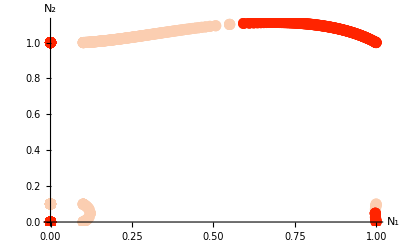

```mathematica
plotTask[1/10,{0,0.002382970637023988,0.019454811603742996,0.2025,0.21},{5,5,100,1}]
```

b = 0.3

```mathematica
N[criticalValuesA[3/10]]
```

{0.01986,0.0504942,0.1225}

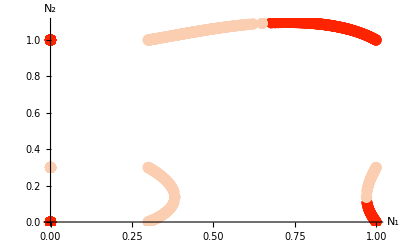

```mathematica
plotTask[3/10,{0,0.01986001392249426,0.050494173879918135,0.1225,0.13},{20,20,90,1}]
```

#### Sequence for b=0.4961661. (Critical Value)

```mathematica
N[criticalValuesA[4961661*10^(-7)]]
```

{0.057545,0.0634621,0.0634621}

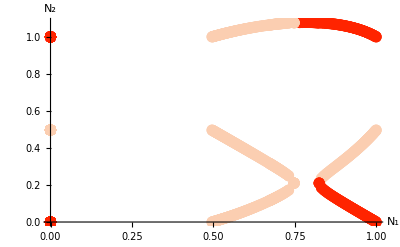

```mathematica
plotTask[4961661*10^(-7),{0,0.057544964217530525,0.06346214969730232,0.064},{50,20,1}]
```

#### Sequence for 0.4961661 < b < 1/2.

b = 0.948

```mathematica
N[criticalValuesA[498/1000]]
```

{0.0586017,0.0628843,0.063001}

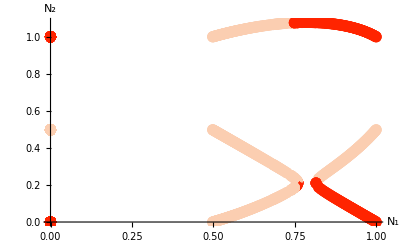

```mathematica
plotTask[498/1000,{0,0.05860173612241946,0.06288434240012102,0.063001,0.064},{50,10,3,1}]
```

#### Sequence for b=1/2. (Critical value)

```mathematica
N[criticalValuesA[1/2]]
```

{0.0610042,0.0625}

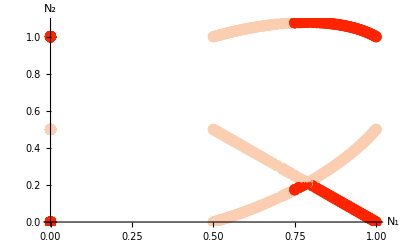

```mathematica
plotTask[1/2,{0,0.0610042339640731,0.0625,0.065},{40,10,1}]
```

#### Sequences for b > 1/2.

b = 0.6

```mathematica
N[criticalValuesA[6/10]]
```

{0.04}

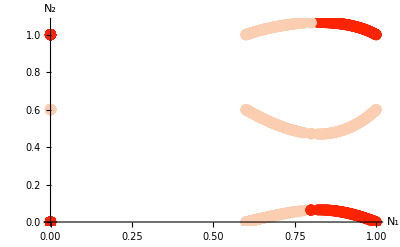

```mathematica
plotTask[6/10,{0,0.04,0.05},{80,1}]
```

b = 0.9

```mathematica
N[criticalValuesA[9/10]]
```

{0.0025}

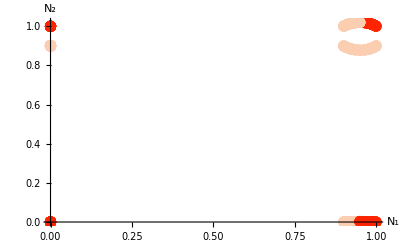

```mathematica
plotTask[9/10,{0,0.0025,0.003},{20,1}]
```

#### End of the file.

#### Source paper: Gergely Röst and AmirHosein Sadeghimanesh, Unidirectional migration of populations with Allee effect.